{{X1→InterpolatingFunction[…],X2→InterpolatingFunction[…],M11→InterpolatingFunction[…],M12→InterpolatingFunction[…],M21→InterpolatingFunction[…],M22→InterpolatingFunction[…]}}

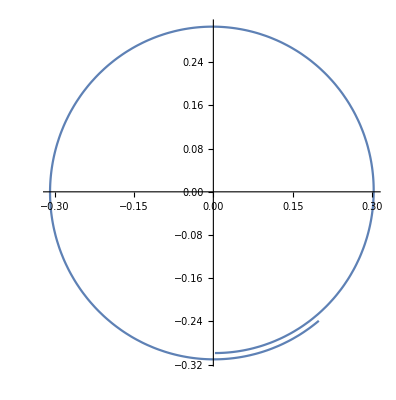

-Graphics-

{0.316228}

5.712

{{0.396342},{-0.77444},{-0.0290587},{1.29654}}

```mathematica
system={X1'[t]==X1[t]/10-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,
X2'[t]==X1[t]+X2[t]/10+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t],
M11'[t]==M11[t]*(-3*X1[t]^2-2*X1[t]*X2[t]-X2[t]^2+1/10)+M21[t]*(-X1[t]^2-2*X1[t]*X2[t]-3*X2[t]^2-1),
M12'[t]==M12[t]*(-3*X1[t]^2-2*X1[t]*X2[t]-X2[t]^2+1/10)+M22[t]*(-X1[t]2-2*X1[t]*X2[t]-3*X2[t]^2-1),
M21'[t]==M11[t]*(3*X1[t]^2-2*X1[t]*X2[t]+X2[t]^2+1)+M21[t]*(-X1[t] ^2+2*X1[t]*X2[t]-3*X2[t]^2+1/10),
M22'[t]==M12[t]*(3*X1[t]^2-2*X1[t]*X2[t]+X2[t]^2+1)+M22[t]*(-X1[t]^2+2*X1[t]*X2[t]-3*X2[t]^2+1/10)};
sol=NDSolve[{system,X1[0]==X2[0]==0.2,M11[0]==M22[0]==1,M12[0]==M21[0]==0},{X1,X2,M11,M12,M21,M22},{t,1000}]
ParametricPlot[Evaluate[{X1[t],X2[t]}/.sol],{t,3.62850988532908,10}]
Plot[Evaluate[M12[t]/.sol],{t,0,1000}]


system1={X1'[t]==X1[t]/10-X2[t]^3-X1[t]*X2[t]^2-X1[t]^2*X2[t]-X2[t]-X1[t]^3,
X2'[t]==X1[t]+X2[t]/10+X1[t]*X2[t]^2+X1[t]^3-X2[t]^3-X1[t]^2*X2[t]};
stableLimitCycleRadius=Sqrt[Evaluate[X1[200]/.sol]^2+Evaluate[X2[200]/.sol]^2]
(*NDSolve[{X1[t]/.sol==tmp,X1[0]==X2[0]==0.2},{X1,X2},{t,50}]*)
{s1,{{x0},{y0}}}=Reap[
NDSolve[{system1,
X1[0]==X2[0]==0.2,WhenEvent[X1'[t]>0,Sow[t,"x"]],(*minima of x*)
WhenEvent[X2'[t]>0,Sow[t,"y"]]},(*minima of y*)
{X1[t],X2[t]},{t,0,50}],{"x","y"}];
tab=Table[Mean@Differences@min[[-Round[Length@min/4];;]],{min,{x0,y0}}];
period=First[tab]

startValue=60;
MforCycle={Evaluate[M11[period]/.sol],Evaluate[M12[period]/.sol],Evaluate[M21[period]/.sol],Evaluate[M22[period]/.sol]}
(*MforCycle={Evaluate[M11[startValue+period]/.sol],Evaluate[M12[startValue+period]/.sol],Evaluate[M21[startValue+period]/.sol],Evaluate[M22[startValue+period]/.sol]}*)
(*FindRoot[(X1[t]^2/.sol+X2[t]^2/.sol)==tmp,{t,1,200}]*)
```

{{r→Function[{t},-ⅇ^(t/10)/(√(10 ⅇ^(t/5)+ⅇ^(2 C[1])))],M11→Function[{t},ⅇ^(1/10 (t-15 Log[10 ⅇ^(t/5)+ⅇ^(2 C[1])])) C[2]],M21→Function[{t},(10 ⅇ^(t/10)+√10 √(10 ⅇ^(t/5)+ⅇ^(2 C[1])))^(-2 √10) C[3]],theta→Function[{t},t+C[4]+1/2 Log[10 ⅇ^(t/5)+ⅇ^(2 C[1])]],M12→Function[{t},C[5]],M22→Function[{t},C[6]]}}

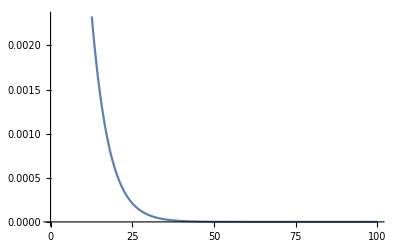

{{M11[t] (1/10-3 r[t]^2),0},{2 M21[t] r[t],0}}

```mathematica
(* Calculations for 1e)*)
firstSystem={r'[t]==r[t]/10-r[t]^3,
theta'[t]== 1+r[t]^2,
M11'[t]== M11[t](1/10-3*r[t]^2),
M12'[t]==0,
M21'[t]== 2M21[t]r[t],
M22'[t]== 0};
solD=DSolve[firstSystem,{r,theta,M11,M12,M21,M22},t]
Plot[Evaluate[M11[t]/.solD/.{C[3]-> 1,C[1]-> 1,C[2]-> 1}],{t,0,100}]

A={r[t],theta[t]};
D[firstSystem,{A}][[2]];

JM={{1/10-3r[t]^2,0},{2r[t],0}}*{{M11[t],M12[t]},{M21[t],M22[t]}}
```

```mathematica
(* Here starts Problem 2*)
system={x'[t]== sigma(y[t]-x[t]),
y'[t]== r*x[t]-y[t]-x[t]z[t],
z'[t]== x[t]y[t]-b* z[t]};
system2=system/.{sigma-> 10,r-> 28,b-> 8/3};
tmp=system2/.(x_== y_)-> y
solForFixed=DSolve[{tmp[[1]]==0,tmp[[2]]==0,tmp[[3]]==0},{x,y,z},t]


sol=NDSolve[{system2,x[0]== y[0]==z[0]== 1},{x,y,z},{t,2000}];

graph=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,1,40},PlotLabel->"Lorenz attractor"];
Show[graph,AxesLabel-> {"x","y","z"}];
variables={x[t],y[t],z[t]};
j=D[system/.(x_== y_)->y,{variables}];
jSystem1=j/.{sigma-> 10,r-> 28,b-> 8/3};
eig=Eigenvalues[jSystem1/.solForFixed[[3]]]

Simplify[eig[[1]]+eig[[2]]+eig[[3]]];
```

{10 (-x[t]+y[t]),28 x[t]-y[t]-x[t] z[t],x[t] y[t]-(8 z[t])/3}

{{x→Function[{t},0],y→Function[{t},0],z→Function[{t},0]},{x→Function[{t},-6 √2],y→Function[{t},-6 √2],z→Function[{t},27]},{x→Function[{t},6 √2],y→Function[{t},6 √2],z→Function[{t},27]}}

{1/3 Root[38880+912 #1+41 #1^2+#1^3&,1],1/3 Root[38880+912 #1+41 #1^2+#1^3&,3],1/3 Root[38880+912 #1+41 #1^2+#1^3&,2]}

```mathematica
Q=IdentityMatrix[3];
jSystem2=j/.{sigma-> 16,r-> 46,b-> 4};
lambda1=0;
lambda2=0;
lambda3=0;
dt=0.0001;
For[i=0,i<100000000,i++,
M=IdentityMatrix[3]+ dt*jSystem1/.t-> 1+i*dt/.sol;
M=M//.{x_List}:>x;
{Q,R}= QRDecomposition[M.Q];

lambda1=lambda1+Log[Abs[R[[1]][[1]]]];
lambda2=lambda2+Log[Abs[R[[2]][[2]]]];
lambda3=lambda3+Log[Abs[R[[3]][[3]]]];
Q=Transpose[Q];
]
lambda1/(i*dt)
lambda2/(i*dt)
lambda3/(i*dt)
```

0.909531

0.00365874

-14.5834

```mathematica
9.64165-1.81107-28.874
N[-16-4-1]
9.64165-1.81107-28.874-
N[-16-4-1]
```

-21.0434

-21.